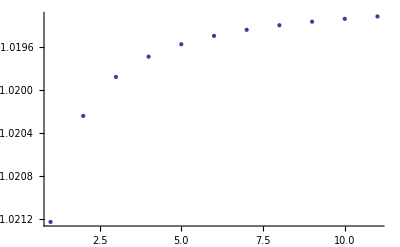

-1.02122
-1.02024
-1.01988
-1.01969
-1.01958
-1.0195
-1.01945
-1.0194
-1.01937
-1.01934
-1.01932

10
19
28
37
46
55
64
73
82
91
100

ListPlot::nonopt: Options expected (instead of -1.02122
-1.02024
-1.01988
-1.01969
-1.01958
-1.0195
-1.01945
-1.0194
-1.01937
-1.01934
« 1 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[10
19
28
37
46
55
64
73
82
91
100,-1.02122
-1.02024
-1.01988
-1.01969
-1.01958
-1.0195
-1.01945
-1.0194
-1.01937
-1.01934
-1.01932]

10
19
28
37
46
55
64
73
82
91
100

ListPlot::nonopt: Options expected (instead of -1.02122
-1.02024
-1.01988
-1.01969
-1.01958
-1.0195
-1.01945
-1.0194
-1.01937
-1.01934
« 1 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[10
19
28
37
46
55
64
73
82
91
100,-1.02122
-1.02024
-1.01988
-1.01969
-1.01958
-1.0195
-1.01945
-1.0194
-1.01937
-1.01934
-1.01932]

```mathematica
Bs1=Table[i,{i,10,100,9}];
d=1.0;
aLam=1.0;
etad1=100.00001;
Bs=Bs1+(1/(3.0*etad1));
aZeta=1.0;
Qm=1.118;
Ep1=8.5;
Em1=85;
akL=(d+aLam);
aOmegD1=1+aLam+((aLam*aLam)/(9*(1+2.0*Bs)));
aOmegD2=((aLam*aLam*Bs)/(9*(1+2.0*Bs)))*(3+aLam);
aOmegD=aOmegD1+aOmegD2;
aF1=(1.0/(1.0+2.0*Bs))+(Bs*(3+aLam)/(1.0+2.0*Bs));
aF2=(d*aLam/(d+aLam))+(d*Bs*(1+aLam)/(1.0+2.0*Bs));
aF31=3.0*d*d/(2.0*aLam*aLam);
aF32=aF1;
E5d=ExpIntegralE[5,d];
aF33=Exp[d]*E5d;
aF3=aF31*(1+aLam+(aLam*aLam*aF32)/3)*aF33;
aF41=(3.0*d*d*Exp[akL]/(2.0*aLam*aLam));
E5kL=ExpIntegralE[5,akL];
E4kL=ExpIntegralE[4,akL];
E3kL=ExpIntegralE[3,akL];
aF42=E5kL;
aF43=aLam*E4kL;
aF44=(aLam*aLam*E3kL)/3;
aF4=aF41*(aF42+aF43+aF44);
FactM=2.0*aZeta/(3.0*aOmegD);
aMob1=FactM*(aF1+aF2+aF3-aF4);


aCapK=1+d+(1.0/(1+d));
G11=Qm/(aLam*aLam*aOmegD);
G12=(aLam*aLam*Ep1)/(3*(Ep1+(Em1*aCapK)));
G13=aF1;
G1=G11*(1+aLam+G12*G13);
aMob2=-G1;

aMob=aMob2;

ListPlot[aMob]
Data1=Column[Re[aMob]]
Data2=Column[Bs1]
ListPlot[Data2,Data1]

L11=(1.0/(1.0+(2.0*Bs)))+((Bs*(3.0+aLam))/(1.0+(2.0*Bs)));
L12=((d*d*d)/(aLam*(d+aLam)))-((d*d)/aLam)+(L11*(1.0+d));
L13=((2.3+(1.7*Bs))/(1.0+Bs));
L14=(1.0+(L13/d))*(1.0+(L13/d))*(1.0+(L13/d));
L14=1.0+(1.0/(2.0*L14));
FactM=2.0*aZeta/(3.0*aOmegD);
aMob3=FactM*L14*L12;

aMob4=aMob2;

Data3=Column[aMob4];
Data4=Column[Bs1]
ListPlot[Data4,Data3]
```

```mathematica
ListPlot[{{0.01}, {0.02}, {0.03}, {0.04}, {0.05}, {0.060000000000000005}, {0.06999999999999999}, {0.08}, {0.09}, {0.09999999999999999}},{{-1.08881792443471}, {-1.0902990705303444}, {-1.0917656891118883}, {-1.0932179928714298}, {-1.0946561903692895}, {-1.0960804861338656}, {-1.0974910807585987}, {-1.0988881709961498}, {-1.1002719498498872}, {-1.1016426066627703}}]
```

ListPlot::nonopt: Options expected (instead of -1.08882
-1.0903
-1.09177
-1.09322
-1.09466
-1.09608
-1.09749
-1.09889
-1.10027
-1.10164) beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[0.01
0.02
0.03
0.04
0.05
0.06
0.07
0.08
0.09
0.1,-1.08882
-1.0903
-1.09177
-1.09322
-1.09466
-1.09608
-1.09749
-1.09889
-1.10027
-1.10164]

```mathematica
ListPlot[{{0.01}, {0.02}, {0.03}, {0.04}, {0.05}, {0.060000000000000005}, {0.06999999999999999}, {0.08}, {0.09}, {0.09999999999999999}},{{-0.13361594686932196}, {-0.13429355887405842}, {-0.13496581426215662}, {-0.13563277630074222}, {-0.13629450726451542}, {-0.13695106845513413}, {-0.1376025202201449}, {-0.13824892197147343}, {-0.13889033220348668}, {-0.13952680851063828}}]
```

ListPlot::nonopt: Options expected (instead of -0.133616
-0.134294
-0.134966
-0.135633
-0.136295
-0.136951
-0.137603
-0.138249
-0.13889
-0.139527) beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[0.01
0.02
0.03
0.04
0.05
0.06
0.07
0.08
0.09
0.1,-0.133616
-0.134294
-0.134966
-0.135633
-0.136295
-0.136951
-0.137603
-0.138249
-0.13889
-0.139527]

```mathematica
ListPlot[{{0.01}, {0.02}, {0.03}, {0.04}, {0.05}, {0.060000000000000005}, {0.06999999999999999}, {0.08}, {0.09}, {0.09999999999999999}},{{-0.4471749060097638}, {-0.4481448692152918}, {-0.4491071647274954}, {-0.4500618831096817}, {-0.45100911350455675}, {-0.45194894366197186}, {-0.4528814599660218}, {-0.4538067474615133}, {-0.45472488987981946}, {-0.45563596966413866}}]
```

ListPlot::nonopt: Options expected (instead of -0.447175
-0.448145
-0.449107
-0.450062
-0.451009
-0.451949
-0.452881
-0.453807
-0.454725
-0.455636) beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[0.01
0.02
0.03
0.04
0.05
0.06
0.07
0.08
0.09
0.1,-0.447175
-0.448145
-0.449107
-0.450062
-0.451009
-0.451949
-0.452881
-0.453807
-0.454725
-0.455636]

```mathematica
ListPlot[{{0.1}, {0.19}, {0.28}, {0.37}, {0.45999999999999996}, {0.5499999999999999}, {0.64}, {0.73}, {0.82}, {0.9099999999999999}, {0.9999999999999999}},{{0.7977856242240986}, {0.8737631896577656}, {0.9322074700857392}, {0.9785598301335284}, {1.0162211223774846}, {1.0474261928735116}, {1.0737041468939457}, {1.0961365465956938}, {1.1155099826145838}, {1.1324102139956218}, {1.147282417551778}}]
```

ListPlot::nonopt: Options expected (instead of 0.797786
0.873763
0.932207
0.97856
1.01622
1.04743
1.0737
1.09614
1.11551
1.13241
« 1 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[0.1
0.19
0.28
0.37
0.46
0.55
0.64
0.73
0.82
0.91
1.,0.797786
0.873763
0.932207
0.97856
1.01622
1.04743
1.0737
1.09614
1.11551
1.13241
1.14728]

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

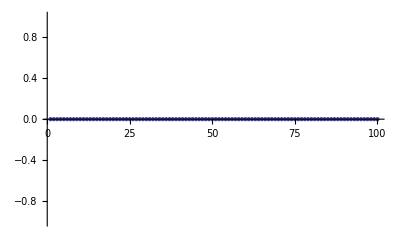

0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.

1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100

ListPlot::nonopt: Options expected (instead of 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
« 50 ») beyond position 3 in TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100,0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.]

```mathematica
ListPlot[{{1.}, {1.9}, {2.8}, {3.7}, {4.6}, {5.5}, {6.4}, {7.3}, {8.2}, {9.1}, {10.}},]
```